```mathematica
u== x^(1/3)y^(2/3)
v== x^(2/3)y^(1/3)
x*p+y*l== w
```

```mathematica
First Consumer
```

```mathematica
Solve[D[x^(1/3)y^(2/3),x]/D[x^(1/3)y^(2/3),y]== p/l,y]
```

{{y→(2 p x)/l}}

```mathematica
Solve[x*p+(2 p x)/l*l== w,x]
```

{{x→w/(3 p)}}

```mathematica
y== Simplify[(2 p *w/(3 p))/l]
```

```mathematica
y==(2 w)/(3 l)
```

```mathematica
Second consumer
```

```mathematica
Solve[D[x^(2/3)y^(1/3),x]/D[x^(2/3)y^(1/3),y]== p/l,y]
```

{{y→(p x)/(2 l)}}

```mathematica
Solve[x*p+(p x)/(2 l)*l== w2,x]
```

{{x→(2 w2)/(3 p)}}

```mathematica
y== Simplify[(p *(2 w2)/(3 p))/(2 l)]
```

y==w2/(3 l)

```mathematica
w2== p+2*l
```

```mathematica
Contract curve
```

```mathematica
D[x^(1/3)y^(2/3),x]/D[x^(1/3)y^(2/3),y]==D[x^(2/3)y^(1/3),x]/D[x^(2/3)y^(1/3),y]
```

y/(2 x)==(2 y)/x

```mathematica
Solve[y/(2 x)==(2 (3-y))/(2-x),y]
```

{{y→(12 x)/(2+3 x)}}

```mathematica
(12 x)/(2+3 x)
```

(12 x)/(2+3 x)

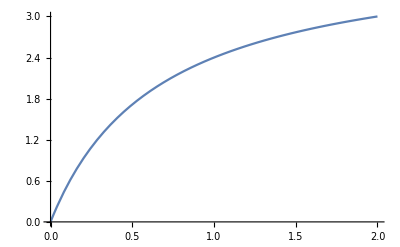

```mathematica
Plot[(12 x)/(2+3 x),{x,0,2},PlotRange->{0,3}]
```

```mathematica
Allocation
```

```mathematica
Solve[(1+l)/3+(2 (1+2*l))/3== 2,l]
```

{{l→3/5}}

```mathematica
(1+l)/3
```